## Measures of “Smoothness” of the graph

### Fourier Transform Measure

#### Depth

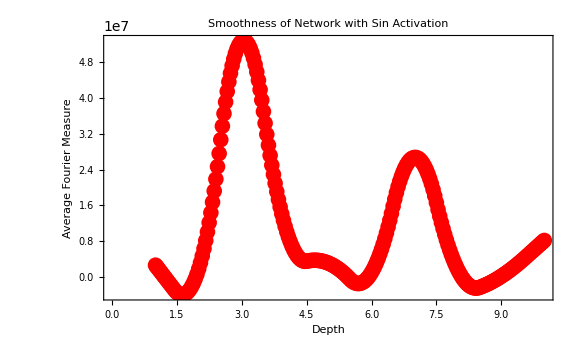

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,1],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
averageSinFourierMeasures=Table[With[{netInit=createAndInitializeNet[depth,Sin]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15 ]]],{depth,depthLevels}];
ListLinePlot[Transpose[{depthLevels,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thin,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large]
```

#### Sin and Sigmoid Together

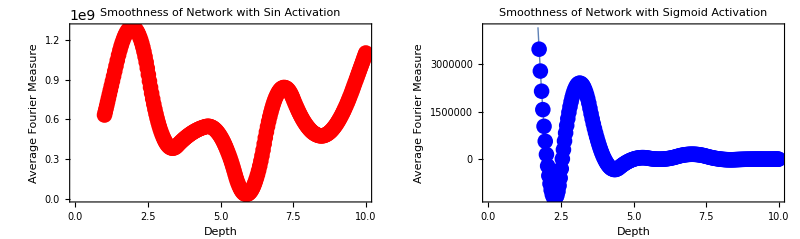

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,2],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
measureFourier[activation_]:=Table[With[{netInit=createAndInitializeNet[depth,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15]]],{depth,depthLevels}];
averageSinFourierMeasures=measureFourier[Sin];
averageSigmoidFourierMeasures=measureFourier[LogisticSigmoid];
sinFourierPlot=ListLinePlot[Transpose[{depthLevels,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidFourierPlot=ListLinePlot[Transpose[{depthLevels,averageSigmoidFourierMeasures}],Frame->True,FrameLabel->{"Depth","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinFourierPlot,sigmoidFourierPlot}}]
```

#### Standard Deviation

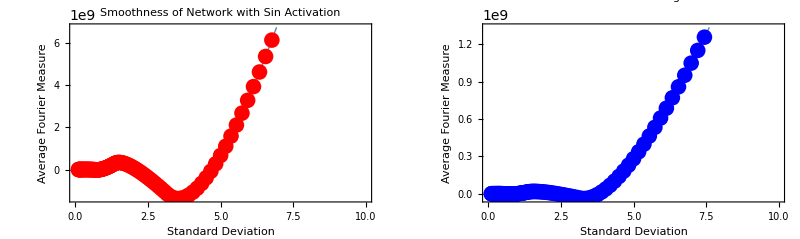

```mathematica
createAndInitializeNet[stdDev_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},3],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
stdDevs={0.1,0.5,1,2,5,10};
measureFourier[activation_]:=Table[With[{netInit=createAndInitializeNet[stdDev,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]],fTransform},fTransform=Abs[Fourier[outputs]];
Total[(Range[0,Length[outputs]-1]^2)*fTransform^2]],15]]],{stdDev,stdDevs}];
averageSinFourierMeasures=measureFourier[Sin];
averageSigmoidFourierMeasures=measureFourier[LogisticSigmoid];
sinFourierPlot=ListLinePlot[Transpose[{stdDevs,averageSinFourierMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidFourierPlot=ListLinePlot[Transpose[{stdDevs,averageSigmoidFourierMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Fourier Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinFourierPlot,sigmoidFourierPlot}}]
```

### Total Variance

#### Depth

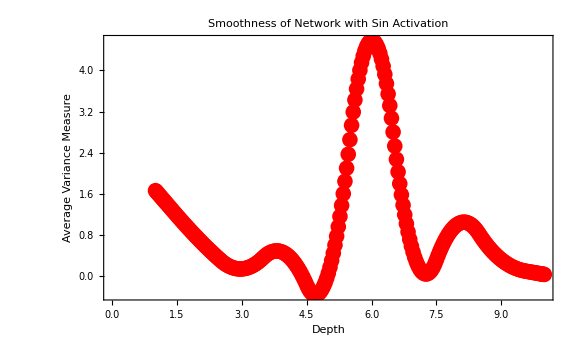

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,1],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
averageSinVarianceMeasures=Table[With[{netInit=createAndInitializeNet[depth,Sin]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15 ]]],{depth,depthLevels}];
ListLinePlot[Transpose[{depthLevels,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large]
```

#### Sin and Sigmoid together

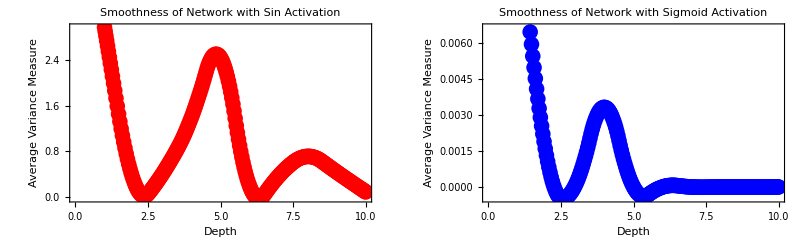

```mathematica
createAndInitializeNet[depth_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},depth],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,1],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
depthLevels=Range[1,10];
measureVariance[activation_]:=Table[With[{netInit=createAndInitializeNet[depth,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{depth,depthLevels}];
averageSinVarianceMeasures=measureVariance[Sin]
averageSigmoidVarianceMeasures=measureVariance[LogisticSigmoid]
sinPlot=ListLinePlot[Transpose[{depthLevels,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidPlot=ListLinePlot[Transpose[{depthLevels,averageSigmoidVarianceMeasures}],Frame->True,FrameLabel->{"Depth","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinPlot,sigmoidPlot}}]
```

#### Standard Deviation

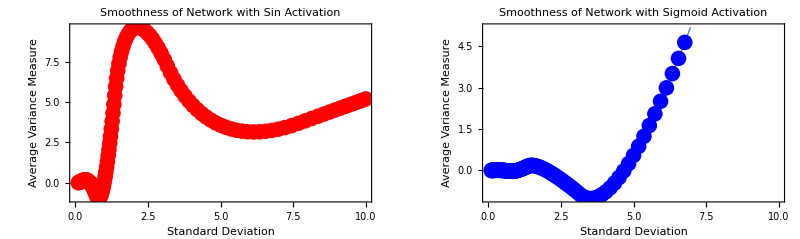

```mathematica
createAndInitializeNet[stdDev_,activation_]:=NetInitialize[NetChain[Append[Catenate@Table[{3,ElementwiseLayer[activation]},3],{}],"Input"->"Real"],Method->{"Random","Weights"->NormalDistribution[0,stdDev],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[0,1]]},RandomSeeding->Automatic];
evaluateNet[net_,x_]:=Module[{f},f[z_?NumericQ]:=net[z];
SetAttributes[f,Listable];
f[x]];
stdDevs={0.1,0.5,1,2,5,10};
measureVariance[activation_]:=Table[With[{netInit=createAndInitializeNet[stdDev,activation]},Mean[Table[Module[{outputs=evaluateNet[netInit,Range[-3,3,0.01]]},Variance[outputs]],15]]],{stdDev,stdDevs}];
averageSinVarianceMeasures=measureVariance[Sin];
averageSigmoidVarianceMeasures=measureVariance[LogisticSigmoid];
sinVariancePlot=ListLinePlot[Transpose[{stdDevs,averageSinVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sin Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Red,ImageSize->Large];
sigmoidVariancePlot=ListLinePlot[Transpose[{stdDevs,averageSigmoidVarianceMeasures}],Frame->True,FrameLabel->{"Standard Deviation","Average Variance Measure"},PlotLabel->"Smoothness of Network with Sigmoid Activation",PlotStyle->Thick,InterpolationOrder->2,Mesh->All,MeshStyle->Blue,ImageSize->Large];
GraphicsGrid[{{sinVariancePlot,sigmoidVariancePlot}}]
```

## Explanation for Above Experiments

The above manipulations of depth and standard deviation were intended to provide a picture of the effect on the “smoothness” of the output graphs generated by 15 runs of a randomly initialized neural network at the depth/std dev combination. Two different activation functions, Sin and Sigmoid, were used because of they completely different output graphs they displayed. Interestingly, for the most part, both the Fourier Measure and the Total Variance graphs for each activation function strongly resembled each other in shape and characteristics, leading to the implication that standard deviation and network depth have similar effects on the output distributions for all types of activation functions, linear and non-linear. This could be because...